## Styling

```mathematica
dir=NotebookDirectory[]
```

/home/nicolas/git/talks/Poster colloque Bouyssy/

```mathematica
(* Thickness *)
th=0.003;
```

```mathematica
(*Styling of the text*)
st=Directive[FontSize->15,FontFamily->"CMU Serif"];
stylize[text_]:=Style[text,st];
```

```mathematica
green=RGBColor["#218b00"];
comp=RGBColor["#8B2300"];
```

```mathematica
SetOptions[ListPlot,Frame->False,FrameStyle->st,PlotRange->All];
```

## Dimensions fractales

```mathematica
(* import données numériques de Rémy *)
{Vs,λs}=Transpose@Import[NotebookDirectory[]<>"approx4180diag_et_lambda.dat"]
```

{{-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.},{100.705,78.7803,72.3462,59.9974,49.1027,39.5811,31.3907,24.471,18.7448,14.12,10.4903,7.73577,5.72272,4.30463,3.33147,2.66861,2.21209,1.89067,1.65863,1.48721,1.35822,1.2599,1.18445,1.12655,1.08248,1.04959,1.02594,1.01012,1.00103,0.997866,1.,1.00695,1.01832,1.03384,1.05326,1.0764,1.10311,1.13327,1.16678,1.20358,1.24359}}

```mathematica
a[z_]:=4 z^2+9z+4;
ωAB[β_]:=(a[E^β]+√(a[E^β]^2-E^(2β)))/E^β;
```

```mathematica
(* the fractal dimensions of a Kalugin-Katz state *)
d[ω_,κ_,q_]:=2/(q-1)Log[ω[2κ]^q/ω[2κ q]]/Log[ω[0]];
```

```mathematica
ds=d[ωAB,#,2.]&/@(0.5Log[λs])
```

{1.20471,1.21158,1.21437,1.22137,1.23041,1.24225,1.25797,1.27904,1.30749,1.34587,1.39696,1.46266,1.54202,1.6294,1.71559,1.79201,1.85409,1.90133,1.93557,1.95943,1.97549,1.98591,1.99239,1.99622,1.99832,1.99937,1.99982,1.99997,2.,2.,2.,1.99999,1.99991,1.9997,1.99928,1.99855,1.99743,1.99583,1.99367,1.99089,1.98744}

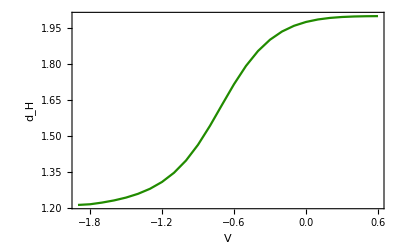

/home/nicolas/git/talks/Poster colloque Bouyssy/dimension_fractale.pdf

```mathematica
ListPlot[MapThread[{#1,#2}&,{Vs,ds}][[2;;-15]],Joined->True,PlotRange->All,Frame->True,PlotStyle->{green},FrameLabel->stylize/@{"V","d_H"}]
Export[NotebookDirectory[]<>"dimension_fractale.pdf",%]
```